```mathematica
<<EEGPack`
```

<<KazukazuM version 0.5.120904 loaded on: Thu 6 Sep 2012 14:41:56>>

```mathematica
tempRadius=20
```

20

## Trying the background with a textured image (Doesn’t reall work well)

```mathematica
tempBk=Rasterize[$FrameBackgroundPlot[PlotRange->{{-70,70},{-70,70}}](*,Background->None*)]
```

-Graphics-

```mathematica
Show[
Graphics3D[
{Texture[tempBk],Polygon[{{-70,-70,0},{-70,70,0},{70,70,0},{70,-70,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}],
}],
ParametricPlot3D[{Cos[t]*($DetectorRadius*Cos[t2]+tempRadius),$DetectorRadius*Sin[t2], Sin[t]*($DetectorRadius*Cos[t2]+tempRadius)},{t,0, Pi}, {t2, 0, 2 Pi}, Axes->True]
]
```

-Graphics3D-

## Trying the background with a textured image

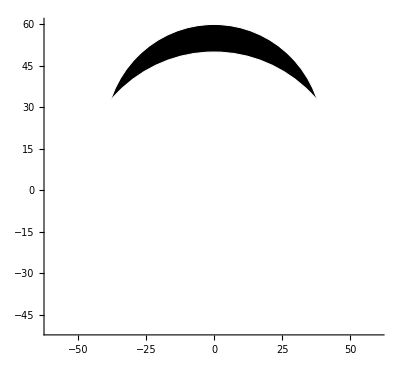

```mathematica
$FrameBackgroundPlot[Axes->True]
```

```mathematica
Show[
ParametricPlot3D[{Cos[theta],Sin[theta],0}*50, {theta,0,2 Pi}, PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10+50,Sin[theta]*10,0}, {theta,-95 Degree,95 Degree}, PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10-50,Sin[theta]*10,0}, {theta,85 Degree,275 Degree}, PlotStyle->Thick],
Graphics3D[{
Thick,Line[{{Cos[-5 Degree]*10,Sin[-5 Degree]*10+50,0},{0,60,0},
{Cos[185 Degree]*10,Sin[185  Degree]*10+50,0}}]
}],
PlotRange->All
]
```

-Graphics3D-

## coherencyArc

```mathematica
coherencyArc[ch1_String,ch2_String, opacity_, color_]:=
Module[{coord1, coord2, vect},
coord1=$GetDetectorCoordinates[ch1];
coord2=$GetDetectorCoordinates[ch2];
vect=coord2-coord1;
coherencyArc[Norm[vect]/2, ArcTan@@vect, (coord1+coord2)/2, opacity, color]
];
```

```mathematica
coherencyArc[radius_,angle_,{x_,y_}, opacity_, color_]:=
ParametricPlot3D[
{{Cos[angle],-Sin[angle],0},{Sin[angle],Cos[angle],0},{0,0,1}}.
{Cos[t]*($DetectorRadius*Cos[t2]+radius),$DetectorRadius*Sin[t2],
 Sin[t]*($DetectorRadius*Cos[t2]+radius)}
+{x,y,0}
,
{t,0, Pi}, {t2 (*tube*), 0, 2 Pi},
PlotStyle->Opacity[opacity, color],
 MeshStyle->None]
```

```mathematica
Show[
ParametricPlot3D[{Cos[theta],Sin[theta],0}*50, {theta,0,2 Pi}, PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10+50,Sin[theta]*10,0}, {theta,-95 Degree,95 Degree}, PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10-50,Sin[theta]*10,0}, {theta,85 Degree,275 Degree}, PlotStyle->Thick],
Graphics3D[{
Thick,Line[{{Cos[-5 Degree]*10,Sin[-5 Degree]*10+50,0},{0,60,0},
{Cos[185 Degree]*10,Sin[185  Degree]*10+50,0}}]
}],
coherencyArc["F8", "Fz",0.25, Red],
Lighting->"Neutral",Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-80,80},{-80,80},{-10,50}}]
```

-Graphics3D-

## coherencyArc multiple

```mathematica
detectors=$DetectorCoordinates[[All,1]];
```

```mathematica
pairs=Subsets[detectors,{2}];
```

```mathematica
Show[
ParametricPlot3D[{Cos[theta],Sin[theta],0}*50, {theta,0,2 Pi}, PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10+50,Sin[theta]*10,0}, {theta,-95 Degree,95 Degree}, PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10-50,Sin[theta]*10,0}, {theta,85 Degree,275 Degree}, PlotStyle->Thick],
Graphics3D[{
Thick,Line[{{Cos[-5 Degree]*10,Sin[-5 Degree]*10+50,0},{0,60,0},
{Cos[185 Degree]*10,Sin[185  Degree]*10+50,0}}]
}],
Table[coherencyArc[n[[1]],n[[2]],RandomReal[{0,0.1}], Hue[RandomReal[{-0.3,0}]]], {n,RandomChoice[pairs,20]}]
,
Lighting->"Neutral",Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-80,80},{-80,80},{-10,50}}]
```

-Graphics3D-

## CoherencyPlot function

```mathematica
Options[$FrameBackgroundPlot3D]=JoinOptionLists[{PlotRange->All},Options[Show]];
```

```mathematica
$FrameBackgroundPlot3D[opts:OptionsPattern[]]:=
Show[
ParametricPlot3D[{Cos[theta],Sin[theta],0}*50, {theta,0,2 Pi},PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10+50,Sin[theta]*10,0}, {theta,-95 Degree,95 Degree}, PlotStyle->Thick],
ParametricPlot3D[{Cos[theta]*10-50,Sin[theta]*10,0}, {theta,85 Degree,275 Degree}, PlotStyle->Thick],
Graphics3D[{
Thick,Line[{{Cos[-5 Degree]*10,Sin[-5 Degree]*10+50,0},{0,60,0},
{Cos[185 Degree]*10,Sin[185  Degree]*10+50,0}}]
}],
Sequence@@JoinOptionLists[Show,{opts},Options[$FrameBackgroundPlot3D]]
];
```

```mathematica
$FrameBackgroundPlot3D[]
```

-Graphics3D-

```mathematica
CoherencyPlotImpl[ch1_String,ch2_String, coherence_]:=
Module[{coord1, coord2, vect},
coord1=$GetDetectorCoordinates[ch1];
coord2=$GetDetectorCoordinates[ch2];
vect=coord2-coord1;
CoherencyPlotImpl[Norm[vect]/2, ArcTan@@vect, (coord1+coord2)/2, coherence]
];
```

```mathematica
CoherencyPlotImpl[radius_,angle_,{x_,y_}, coherence_]:=
Module[{temp,fact, rad},
fact=Abs[Arg[coherence]]/Pi;
rad=$DetectorRadius*Abs[coherence];
ParametricPlot3D[
{{Cos[angle],-Sin[angle],0},{Sin[angle],Cos[angle],0},{0,0,1}}.
{Cos[t]*(rad*Cos[t2]+radius),rad*Sin[t2],
 Sin[t]*(rad*Cos[t2]+radius)}
+{x,y,0},
{t,0,  Pi}, {t2 (*tube*), 0, 2 Pi},
ColorFunctionScaling->False,
ColorFunction->If[Arg[coherence]≥ 0,
Function[{xf,yf,z,u,v},Hue[-u/Pi/3,1,fact,(Abs[N[coherence]]*1-0.75)*4]],
Function[{xf,yf,z,u,v},Hue[(u/Pi-1)/3,1,fact,(Abs[N[coherence]]*1-0.75)*4]]   ](*If*),
(*PlotStyle->Opacity[Abs[coherence]*1],*)
 MeshStyle->None
](*ParametricPlot3D*)
];
```

```mathematica
Options[CoherencyPlot]=Options[Graphics3D];
```

```mathematica
CoherencyPlot[coherencies_List, pairs_List, opts:OptionsPattern[]]:=
Module[{cohPairs},
cohPairs=Flatten/@Transpose[{pairs,coherencies}];
cohPairs=Select[cohPairs,Abs[#[[3]]]>0.75&];
Show[
Sequence@@Table[CoherencyPlotImpl[n[[1]],n[[2]],n[[3]]], {n,cohPairs}],
$FrameBackgroundPlot3D[],
Sequence@@JoinOptionLists[Show,
{opts},{Lighting->"Neutral",PlotRange->{{-65,65},{-65,65},{-10,50}},
BaseStyle->{FontFamily->"Helvetica"}},Options[CoherencyPlot]
]
]
];
```

```mathematica
Show[
$FrameBackgroundPlot3D[],
CoherencyPlotImpl["F8","Cz",0.9 ⅇ^((30.  Degree)/2*ⅈ)],
Lighting->"Neutral",Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-80,80},{-80,80},{-30,50}}]
```

-Graphics3D-